```mathematica
dat=ReadList["/home/amer/Grive/Programacio/C/FEM/tfgfem-1.0.0/demos/fem2d/demo05/demo05.txt",Number,RecordLists->True];
```

```mathematica
ListPlot3D[dat,Mesh->All,InterpolationOrder->1,ColorFunction->"ThermometerColors",MeshStyle->{Gray,Opacity[0.1]}]
```

-Graphics3D-

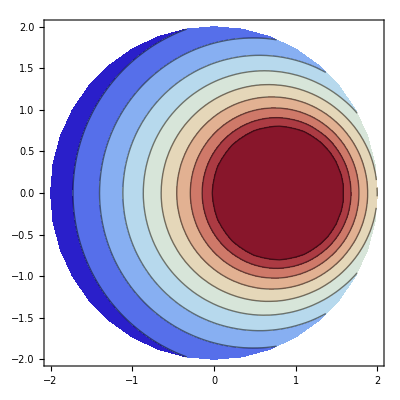

```mathematica
ListContourPlot[dat,ColorFunction->"ThermometerColors"]
```